### Fourier Transform

```mathematica
Subscript[ϕ, b][x_,t_]=-ϕ[x,t]+ϕ[x,t]^3-ϵ^2*D[ϕ[x,t],{x,2}];
eq1=D[ϕ[x,t], t] == Dϕ*D[Subscript[A, b]*(2*Subscript[ϕ, b][x,t]*(-1+3*ϕ[x,t]^2-2*ϵ*β*u[x,t]^2*ϕ[x,t])-2*ϵ^2*D[Subscript[ϕ, b][x,t],{x,2}])+4 Subscript[A, s]*ϕ[x,t]*(ϕ[x,t]^2-1)*u[x,t]^2*(u[x,t]-umax)^2+ 2 Subscript[A, f]*ϕ[x,t]*u[x,t]^2-2*σ*(u[x,t]^2*D[ϕ[x,t], {x,2}]+2*u[x,t]*D[u[x,t],x]*D[ϕ[x,t],x]),{x,2}]+kH*D[u[x,t],{x,2}];

eq2=D[u[x,t],t]== Du*D[Subscript[A, b]*4*ϵ*β*u[x,t]*(1-ϕ[x,t]^2)*Subscript[ϕ, b][x,t]+2*Subscript[A, s]*((u[x,t]*(u[x,t]-umax)*(2*u[x,t]-umax))*(ϕ[x,t]^2-1)^2-λ*D[u[x,t],{x,2}])+2*Subscript[A, f] ϕ[x,t]^2*u[x,t],{x,2}]+Subscript[λ, 1]*D[D[ϕ[x,t],{x,2}]*u[x,t]+2*σ*u[x,t]*D[ϕ[x,t],x]^2,{x,2}]+kH*D[ϕ[x,t],{x,2}]+v0*D[u[x,t]^2*D[ϕ[x,t],x],x];

rules={ϕ->Function[{x,t},Subscript[ϕ, 0]+δ*Subscript[ϕ, 1][x,t]],u->Function[{x,t},Subscript[u, 0]+δ*Subscript[u, 1][x,t]]};
rhs1=eq1[[2]]/.rules//Expand;
rhs2=eq2[[2]]/.rules//Expand;


(*Algebraic simplification*)
rhs1=Expand[rhs1]//Simplify;
rhs2=Expand[rhs2]//Simplify;

(*First-order terms*)
lin1=Coefficient[rhs1,δ,1]//Simplify;
lin2=Coefficient[rhs2,δ,1]//Simplify;

fourierRules={D[Subscript[ϕ, 1][x,t],x]->I*k*Subscript[ϕ, 1][x,t],D[Subscript[u, 1][x,t],x]->I*k*Subscript[u, 1][x,t],D[Subscript[ϕ, 1][x,t],{x,2}]->-k^2*Subscript[ϕ, 1][x,t],D[Subscript[u, 1][x,t],{x,2}]->-k^2*Subscript[u, 1][x,t],D[Subscript[ϕ, 1][x,t],{x,3}]->-I*k^3*Subscript[ϕ, 1][x,t],D[Subscript[u, 1][x,t],{x,3}]->-I*k^3*Subscript[u, 1][x,t],D[Subscript[ϕ, 1][x,t],{x,4}]->k^4*Subscript[ϕ, 1][x,t],D[Subscript[u, 1][x,t],{x,4}]->k^4*Subscript[u, 1][x,t]};
lin1k=lin1/.fourierRules//Simplify;
lin2k=lin2/.fourierRules//Simplify;

vars={Subscript[ϕ, 1][x,t],Subscript[u, 1][x,t]};
J=Outer[D,{lin1k,lin2k},vars]//Simplify;
Eigenvalues[J];
```

### Plot

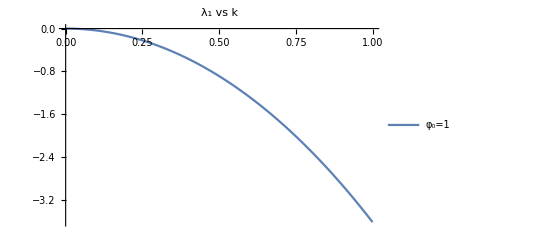

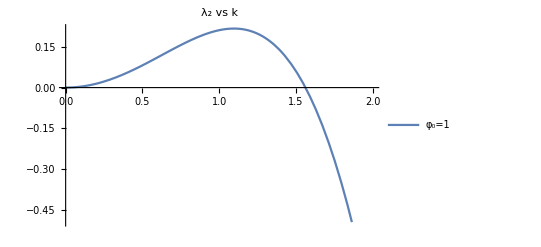

```mathematica
params={Subscript[A, s]->1,Subscript[A, f]->6,umax->2,σ->1,λ->0.,Subscript[λ, 1]->0.1,Du->0.1,Dϕ->0.05,Subscript[u, 0]->1.5,ϵ-> 0.2, β-> 0.1, Subscript[A, b]->1.0, kH-> -0.2, v0 ->- 0.5};
Jnum=J/.params;

eig[k_?NumericQ,phi_?NumericQ]:=Eigenvalues[N[Jnum/.Subscript[ϕ, 0]->phi]];
eig1[k_?NumericQ,phi_?NumericQ]:=eig[k,phi][[1]];
eig2[k_?NumericQ,phi_?NumericQ]:=eig[k,phi][[2]];
phiVals={1};

Plot[Evaluate@Table[Re[eig1[k,phiVals[[i]]]],{i,Length[phiVals]}],{k,0,1},PlotLegends->Table["φ_0="<>ToString[phiVals[[i]]],{i,Length[phiVals]}],PlotLabel->"λ_1 vs k"]

Plot[Evaluate@Table[Re[eig2[k,phiVals[[i]]]],{i,Length[phiVals]}],{k,0,2},PlotLegends->Table["φ_0="<>ToString[phiVals[[i]]],{i,Length[phiVals]}],PlotLabel->"λ_2 vs k"]
```

```mathematica
params={k->7,Subscript[ϕ, 0]->0};
Jnum2=Jnum/.params
```

{{0.8624,24.5},{0,0}}

```mathematica
params={k->1,Subscript[ϕ, 0]->0};
Jnum2=Jnum/.params
```

{{0.2696,0.},{0.,1.4}}

```mathematica
params={Subscript[A, s]->2,Subscript[A, f]->2,umax->3,σ->1,λ->1.0,Subscript[λ, 1]->0.,Du->0.1,Dϕ->0.01,Subscript[u, 0]->1.5,ϵ-> 0.01, β->0.2, Subscript[A, b]->0.02};

Jnum=J/.params

eig[k_,phi_]:=SortBy[Eigenvalues[N[Jnum/.{Subscript[ϕ, 0]->phi,k->k}]],Re];

kVals=Range[0,4,0.01];
phiVals={-0.};

data=Flatten[Table[With[{ev=eig[k,phi]},{k,phi,Re[ev[[1]]],Re[ev[[2]]]}],{phi,phiVals},{k,kVals}],1];

Export["/home/soumyadeep/Desktop/Active_Gel/My_Codes/02a_eigen_data.csv",N[data]]
```

{{-0.02 k^2 (4.5+2.25 k^2+20.25 (-1+3 ϕ_0^2)+0.02 (1-12 ϕ_0^2+15 ϕ_0^4)),-0.12 k^2 ϕ_0},{-1.5 k^2 (0.+0.8 ϕ_0),-0.2 k^2 (2 ϕ_0^2+2 (9+1. k^2-18 ϕ_0^2+9 ϕ_0^4-13.5 (-1+ϕ_0^2)^2))}}

/home/soumyadeep/Desktop/Active_Gel/My_Codes/02a_eigen_data.csv